```mathematica
{{data = Import["E:\\Alessio\\Desktop\\Computazionale\\es14_oscillatore_armonico_semplice\\data.txt","Table"]}, {}};
```

```mathematica
X = Take[data][[All, {1,2}]]
V = Take[data][[All, {1,3}]]
K = Take[data][[All , {2,3}]]
Xk2 = Take[data][[All, {1,4}]]
Vk2 = Take[data][[All, {1,5}]]
Kk2 = Take[data][[All , {4,5}]]
Xk4 = Take[data][[All, {1,6}]]
Vk4 = Take[data][[All, {1,7}]]
Kk4 = Take[data][[All , {6,7}]]
DX = Take[data][[All, {1,8}]]
DV = Take[data][[All, {1,9}]]
DXk2 = Take[data][[All, {1,10}]]
DVk2 = Take[data][[All, {1,11}]]
DXk4 = Take[data][[All, {1,12}]]
DVk4 = Take[data][[All, {1,13}]]
XT = Take[data][[All, {1,14}]]
VT = Take[data][[All, {1,15}]]
KT = Take[data][[All, {14,15}]]
DK = Take[data][[All, {8,9}]]
DKk2 = Take[data][[All, {10,11}]]
DKk4 = Take[data][[All, {12,13}]]
```

{{0.,0.},{0.2,0.2},{0.4,0.4},{0.6,0.592},{0.8,0.768},{1.,0.92032},{1.2,1.04192},{1.4,1.12671},{1.6,1.16982},{1.8,1.16786},{2.,1.11911},{2.2,1.02364},{2.4,0.883415},{2.6,0.70224},{2.8,0.485728},{3.,0.241127},{3.2,-0.022904},{3.4,-0.296579},{3.6,-0.569339},{3.8,-0.830235},{4.,-1.06836},{4.2,-1.27327},{4.4,-1.43545},{4.6,-1.5467},{4.8,-1.60053},{5.,-1.59249},{5.2,-1.52043},{5.4,-1.38467},{5.6,-1.1881},{5.8,-0.936134},{6.,-0.636648},{6.2,-0.299716},{6.4,0.062682},{6.6,0.437068},{6.8,0.808947},{7.,1.16334},{7.2,1.48538},{7.4,1.76089},{7.6,1.97698},{7.8,2.12263},{8.,2.18921},{8.2,2.17088},{8.4,2.06498},{8.6,1.87224},{8.8,1.59691},{9.,1.24669},{9.2,0.832589},{9.4,0.368623},{9.6,-0.128647},{9.8,-0.640661},{10.,-1.14753},{10.2,-1.62877},{10.4,-2.06411},{10.6,-2.4343},{10.8,-2.72193},{11.,-2.91218},{11.2,-2.99356},{11.4,-2.95845},{11.6,-2.8036},{11.8,-2.5304},{12.,-2.14507},{12.2,-1.65852},{12.4,-1.08616},{12.6,-0.447469},{12.8,0.234672},{13.,0.934713},{13.2,1.62537},{13.4,2.27863},{13.6,2.86688},{13.8,3.36399},{14.,3.74642},{14.2,3.99429},{14.4,4.0923},{14.6,4.03054},{14.8,3.80509},{15.,3.41842},{15.2,2.87955},{15.4,2.20393},{15.6,1.41314},{15.8,0.534189},{16.,-0.401288},{16.2,-1.35813},{16.4,-2.29893},{16.6,-3.18539},{16.8,-3.9799},{17.,-4.647},{17.2,-5.1549},{17.4,-5.47691},{17.6,-5.59274},{17.8,-5.48948},{18.,-5.16252},{18.2,-4.61598},{18.4,-3.86293},{18.6,-2.92525},{18.8,-1.83305},{19.,-0.623842},{19.2,0.65869},{19.4,1.96618},{19.6,3.24731},{19.8,4.44981}}

{{0.,1.},{0.2,1.},{0.4,0.96},{0.6,0.88},{0.8,0.7616},{1.,0.608},{1.2,0.423936},{1.4,0.215552},{1.6,-0.009789},{1.8,-0.243753},{2.,-0.477325},{2.2,-0.701147},{2.4,-0.905876},{2.6,-1.08256},{2.8,-1.22301},{3.,-1.32015},{3.2,-1.36838},{3.4,-1.3638},{3.6,-1.30448},{3.8,-1.19061},{4.,-1.02457},{4.2,-0.810895},{4.4,-0.556241},{4.6,-0.269151},{4.8,0.040189},{5.,0.360294},{5.2,0.678792},{5.4,0.982879},{5.6,1.25981},{5.8,1.49743},{6.,1.68466},{6.2,1.81199},{6.4,1.87193},{6.6,1.8594},{6.8,1.77198},{7.,1.61019},{7.2,1.37752},{7.4,1.08045},{7.6,0.72827},{7.8,0.332875},{8.,-0.091652},{8.2,-0.529493},{8.4,-0.963668},{8.6,-1.37666},{8.8,-1.75111},{9.,-2.07049},{9.2,-2.31983},{9.4,-2.48635},{9.6,-2.56007},{9.8,-2.53435},{10.,-2.40621},{10.2,-2.17671},{10.4,-1.85095},{10.6,-1.43813},{10.8,-0.951268},{11.,-0.406882},{11.2,0.175555},{11.4,0.774267},{11.6,1.36596},{11.8,1.92668},{12.,2.43276},{12.2,2.86177},{12.4,3.19347},{12.6,3.41071},{12.8,3.5002},{13.,3.45327},{13.2,3.26632},{13.4,2.94125},{13.6,2.48552},{13.8,1.91215},{14.,1.23935},{14.2,0.490068},{14.4,-0.308789},{14.6,-1.12725},{14.8,-1.93336},{15.,-2.69438},{15.2,-3.37806},{15.4,-3.95397},{15.6,-4.39476},{15.8,-4.67738},{16.,-4.78422},{16.2,-4.70396},{16.4,-4.43234},{16.6,-3.97255},{16.8,-3.33547},{17.,-2.53949},{17.2,-1.61009},{17.4,-0.579114},{17.6,0.516269},{17.8,1.63482},{18.,2.73271},{18.2,3.76522},{18.4,4.68841},{18.6,5.461},{18.8,6.04605},{19.,6.41266},{19.2,6.53743},{19.4,6.40569},{19.6,6.01246},{19.8,5.36299}}

{{0.,1.},{0.2,1.},{0.4,0.96},{0.592,0.88},{0.768,0.7616},{0.92032,0.608},{1.04192,0.423936},{1.12671,0.215552},{1.16982,-0.009789},{1.16786,-0.243753},{1.11911,-0.477325},{1.02364,-0.701147},{0.883415,-0.905876},{0.70224,-1.08256},{0.485728,-1.22301},{0.241127,-1.32015},{-0.022904,-1.36838},{-0.296579,-1.3638},{-0.569339,-1.30448},{-0.830235,-1.19061},{-1.06836,-1.02457},{-1.27327,-0.810895},{-1.43545,-0.556241},{-1.5467,-0.269151},{-1.60053,0.040189},{-1.59249,0.360294},{-1.52043,0.678792},{-1.38467,0.982879},{-1.1881,1.25981},{-0.936134,1.49743},{-0.636648,1.68466},{-0.299716,1.81199},{0.062682,1.87193},{0.437068,1.8594},{0.808947,1.77198},{1.16334,1.61019},{1.48538,1.37752},{1.76089,1.08045},{1.97698,0.72827},{2.12263,0.332875},{2.18921,-0.091652},{2.17088,-0.529493},{2.06498,-0.963668},{1.87224,-1.37666},{1.59691,-1.75111},{1.24669,-2.07049},{0.832589,-2.31983},{0.368623,-2.48635},{-0.128647,-2.56007},{-0.640661,-2.53435},{-1.14753,-2.40621},{-1.62877,-2.17671},{-2.06411,-1.85095},{-2.4343,-1.43813},{-2.72193,-0.951268},{-2.91218,-0.406882},{-2.99356,0.175555},{-2.95845,0.774267},{-2.8036,1.36596},{-2.5304,1.92668},{-2.14507,2.43276},{-1.65852,2.86177},{-1.08616,3.19347},{-0.447469,3.41071},{0.234672,3.5002},{0.934713,3.45327},{1.62537,3.26632},{2.27863,2.94125},{2.86688,2.48552},{3.36399,1.91215},{3.74642,1.23935},{3.99429,0.490068},{4.0923,-0.308789},{4.03054,-1.12725},{3.80509,-1.93336},{3.41842,-2.69438},{2.87955,-3.37806},{2.20393,-3.95397},{1.41314,-4.39476},{0.534189,-4.67738},{-0.401288,-4.78422},{-1.35813,-4.70396},{-2.29893,-4.43234},{-3.18539,-3.97255},{-3.9799,-3.33547},{-4.647,-2.53949},{-5.1549,-1.61009},{-5.47691,-0.579114},{-5.59274,0.516269},{-5.48948,1.63482},{-5.16252,2.73271},{-4.61598,3.76522},{-3.86293,4.68841},{-2.92525,5.461},{-1.83305,6.04605},{-0.623842,6.41266},{0.65869,6.53743},{1.96618,6.40569},{3.24731,6.01246},{4.44981,5.36299}}

{{0.,0.},{0.2,0.2},{0.4,0.392},{0.6,0.56824},{0.8,0.721594},{1.,0.845856},{1.2,0.935996},{1.4,0.988357},{1.6,1.00081},{1.8,0.972835},{2.,0.905547},{2.2,0.801647},{2.4,0.665319},{2.6,0.502058},{2.8,0.318448},{3.,0.1219},{3.2,-0.079652},{3.4,-0.278066},{3.6,-0.465326},{3.8,-0.633862},{4.,-0.776857},{4.2,-0.888524},{4.4,-0.96434},{4.6,-1.00123},{4.8,-0.997678},{5.,-0.953822},{5.2,-0.871414},{5.4,-0.753768},{5.6,-0.605623},{5.8,-0.432951},{6.,-0.242719},{6.2,-0.042606},{6.4,0.15931},{6.6,0.35487},{6.8,0.536171},{7.,0.695884},{7.2,0.827546},{7.4,0.925829},{7.6,0.986747},{7.8,1.00783},{8.,0.988196},{8.2,0.928635},{8.4,0.831534},{8.6,0.7008},{8.8,0.541702},{9.,0.360655},{9.2,0.164965},{9.4,-0.037468},{9.6,-0.238468},{9.8,-0.429914},{10.,-0.604069},{10.2,-0.753888},{10.4,-0.873311},{10.6,-0.957499},{10.8,-1.00304},{11.,-1.00807},{11.2,-0.972384},{11.4,-0.897395},{11.6,-0.786123},{11.8,-0.643046},{12.,-0.473933},{12.2,-0.285605},{12.4,-0.085664},{12.6,0.117818},{12.8,0.316622},{13.,0.502713},{13.2,0.66857},{13.4,0.807482},{13.6,0.913828},{13.8,0.983298},{14.,1.01307},{14.2,1.00193},{14.4,0.9503},{14.6,0.860262},{14.8,0.735432},{15.,0.580841},{15.2,0.402722},{15.4,0.208263},{15.6,0.005311},{15.8,-0.197936},{16.,-0.393268},{16.2,-0.57279},{16.4,-0.729243},{16.6,-0.856298},{16.8,-0.948808},{17.,-1.00302},{17.2,-1.01674},{17.4,-0.989384},{17.6,-0.922046},{17.8,-0.817431},{18.,-0.67975},{18.2,-0.514552},{18.4,-0.3285},{18.6,-0.129102},{18.8,0.075592},{19.,0.277313},{19.2,0.467912},{19.4,0.639683},{19.6,0.78568},{19.8,0.899993}}

{{0.,1.},{0.2,0.98},{0.4,0.9204},{0.6,0.823592},{0.8,0.693472},{1.,0.535284},{1.2,0.355407},{1.4,0.1611},{1.6,-0.039794},{1.8,-0.23916},{2.,-0.428944},{2.2,-0.601474},{2.4,-0.749774},{2.6,-0.867842},{2.8,-0.950897},{3.,-0.995569},{3.2,-1.00004},{3.4,-0.964106},{3.6,-0.889211},{3.8,-0.778361},{4.,-0.636022},{4.2,-0.46793},{4.4,-0.280867},{4.6,-0.082381},{4.8,0.119512},{5.,0.316657},{5.2,0.501088},{5.4,0.665349},{5.6,0.802796},{5.8,0.907865},{6.,0.976298},{6.2,1.00532},{6.4,0.99373},{6.6,0.941994},{6.8,0.85218},{7.,0.727902},{7.2,0.574168},{7.4,0.397175},{7.6,0.204066},{7.8,0.002635},{8.,-0.198983},{8.2,-0.392642},{8.4,-0.570517},{8.6,-0.725413},{8.8,-0.851065},{9.,-0.942384},{9.2,-0.995667},{9.4,-1.00875},{9.6,-0.981078},{9.8,-0.913763},{10.,-0.809505},{10.2,-0.672501},{10.4,-0.508273},{10.6,-0.323446},{10.8,-0.125477},{11.,0.07764},{11.2,0.277702},{11.4,0.466625},{11.6,0.636771},{11.8,0.78126},{12.,0.894244},{12.2,0.971146},{12.4,1.00884},{12.6,1.0058},{12.8,0.962121},{13.,0.879554},{13.2,0.76142},{13.4,0.612478},{13.6,0.438732},{13.8,0.247191},{14.,0.045588},{14.2,-0.157938},{14.4,-0.355165},{14.6,-0.538121},{14.8,-0.699411},{15.,-0.832509},{15.2,-0.932027},{15.4,-0.993931},{15.6,-1.01571},{15.8,-0.996453},{16.,-0.936937},{16.2,-0.839545},{16.4,-0.708196},{16.6,-0.548183},{16.8,-0.36596},{17.,-0.168879},{17.2,0.035103},{17.4,0.237749},{17.6,0.430871},{17.8,0.606663},{18.,0.758016},{18.2,0.878806},{18.4,0.96414},{18.6,1.01056},{18.8,1.01617},{19.,0.980725},{19.2,0.905648},{19.4,0.793952},{19.6,0.650137},{19.8,0.479998}}

{{0.,1.},{0.2,0.98},{0.392,0.9204},{0.56824,0.823592},{0.721594,0.693472},{0.845856,0.535284},{0.935996,0.355407},{0.988357,0.1611},{1.00081,-0.039794},{0.972835,-0.23916},{0.905547,-0.428944},{0.801647,-0.601474},{0.665319,-0.749774},{0.502058,-0.867842},{0.318448,-0.950897},{0.1219,-0.995569},{-0.079652,-1.00004},{-0.278066,-0.964106},{-0.465326,-0.889211},{-0.633862,-0.778361},{-0.776857,-0.636022},{-0.888524,-0.46793},{-0.96434,-0.280867},{-1.00123,-0.082381},{-0.997678,0.119512},{-0.953822,0.316657},{-0.871414,0.501088},{-0.753768,0.665349},{-0.605623,0.802796},{-0.432951,0.907865},{-0.242719,0.976298},{-0.042606,1.00532},{0.15931,0.99373},{0.35487,0.941994},{0.536171,0.85218},{0.695884,0.727902},{0.827546,0.574168},{0.925829,0.397175},{0.986747,0.204066},{1.00783,0.002635},{0.988196,-0.198983},{0.928635,-0.392642},{0.831534,-0.570517},{0.7008,-0.725413},{0.541702,-0.851065},{0.360655,-0.942384},{0.164965,-0.995667},{-0.037468,-1.00875},{-0.238468,-0.981078},{-0.429914,-0.913763},{-0.604069,-0.809505},{-0.753888,-0.672501},{-0.873311,-0.508273},{-0.957499,-0.323446},{-1.00304,-0.125477},{-1.00807,0.07764},{-0.972384,0.277702},{-0.897395,0.466625},{-0.786123,0.636771},{-0.643046,0.78126},{-0.473933,0.894244},{-0.285605,0.971146},{-0.085664,1.00884},{0.117818,1.0058},{0.316622,0.962121},{0.502713,0.879554},{0.66857,0.76142},{0.807482,0.612478},{0.913828,0.438732},{0.983298,0.247191},{1.01307,0.045588},{1.00193,-0.157938},{0.9503,-0.355165},{0.860262,-0.538121},{0.735432,-0.699411},{0.580841,-0.832509},{0.402722,-0.932027},{0.208263,-0.993931},{0.005311,-1.01571},{-0.197936,-0.996453},{-0.393268,-0.936937},{-0.57279,-0.839545},{-0.729243,-0.708196},{-0.856298,-0.548183},{-0.948808,-0.36596},{-1.00302,-0.168879},{-1.01674,0.035103},{-0.989384,0.237749},{-0.922046,0.430871},{-0.817431,0.606663},{-0.67975,0.758016},{-0.514552,0.878806},{-0.3285,0.96414},{-0.129102,1.01056},{0.075592,1.01617},{0.277313,0.980725},{0.467912,0.905648},{0.639683,0.793952},{0.78568,0.650137},{0.899993,0.479998}}

{{0.,0.},{0.2,0.198667},{0.4,0.389413},{0.6,0.564635},{0.8,0.717347},{1.,0.841462},{1.2,0.932031},{1.4,0.985444},{1.6,0.999571},{1.8,0.973849},{2.,0.909304},{2.2,0.808509},{2.4,0.675483},{2.6,0.515528},{2.8,0.335021},{3.,0.141158},{3.2,-0.058332},{3.4,-0.255496},{3.6,-0.442474},{3.8,-0.611813},{4.,-0.756761},{4.2,-0.871541},{4.4,-0.951575},{4.6,-0.993674},{4.8,-0.99616},{5.,-0.958932},{5.2,-0.883477},{5.4,-0.7728},{5.6,-0.631316},{5.8,-0.464664},{6.,-0.279488},{6.2,-0.083169},{6.4,0.116464},{6.6,0.311454},{6.8,0.494028},{7.,0.656907},{7.2,0.793598},{7.4,0.898651},{7.6,0.967878},{7.8,0.998521},{8.,0.989356},{8.2,0.94075},{8.4,0.85464},{8.6,0.73446},{8.8,0.585},{9.,0.412218},{9.2,0.223003},{9.4,0.024898},{9.6,-0.174199},{9.8,-0.366351},{10.,-0.543899},{10.2,-0.699763},{10.4,-0.827731},{10.6,-0.9227},{10.8,-0.980885},{11.,-0.999967},{11.2,-0.979183},{11.4,-0.919364},{11.6,-0.822894},{11.8,-0.693619},{12.,-0.536692},{12.2,-0.358369},{12.4,-0.16576},{12.6,0.033457},{12.8,0.23134},{13.,0.42},{13.2,0.591916},{13.4,0.740236},{13.6,0.859045},{13.8,0.943607},{14.,0.990552},{14.2,0.998007},{14.4,0.965676},{14.6,0.894848},{14.8,0.788346},{15.,0.650416},{15.2,0.486557},{15.4,0.303301},{15.6,0.107954},{15.8,-0.091697},{16.,-0.287692},{16.2,-0.472217},{16.4,-0.637918},{16.6,-0.778187},{16.8,-0.887432},{17.,-0.9613},{17.2,-0.996844},{17.4,-0.992649},{17.6,-0.948881},{17.8,-0.867285},{18.,-0.751114},{18.2,-0.604999},{18.4,-0.434766},{18.6,-0.2472},{18.8,-0.04978},{19.,0.149624},{19.2,0.343063},{19.4,0.522826},{19.6,0.681746},{19.8,0.813487}}

{{0.,1.},{0.2,0.980067},{0.4,0.921062},{0.6,0.825339},{0.8,0.696713},{1.,0.540312},{1.2,0.362371},{1.4,0.169985},{1.6,-0.029178},{1.8,-0.227178},{2.,-0.416121},{2.2,-0.588475},{2.4,-0.737368},{2.6,-0.856866},{2.8,-0.942204},{3.,-0.98998},{3.2,-0.99829},{3.4,-0.966802},{3.6,-0.896772},{3.8,-0.790992},{4.,-0.653678},{4.2,-0.490304},{4.4,-0.307385},{4.6,-0.112211},{4.8,0.087435},{5.,0.283596},{5.2,0.468451},{5.4,0.63463},{5.6,0.77551},{5.8,0.885473},{6.,0.960136},{6.2,0.996522},{6.4,0.993181},{6.6,0.950246},{6.8,0.869429},{7.,0.753951},{7.2,0.608417},{7.4,0.438628},{7.6,0.251352},{7.8,0.054057},{8.,-0.145393},{8.2,-0.339047},{8.4,-0.519185},{8.6,-0.678624},{8.8,-0.81101},{9.,-0.911063},{9.2,-0.974797},{9.4,-0.999669},{9.6,-0.984689},{9.8,-0.930453},{10.,-0.839124},{10.2,-0.714343},{10.4,-0.561085},{10.6,-0.385458},{10.8,-0.194465},{11.,0.004281},{11.2,0.202856},{11.4,0.393343},{11.6,0.56815},{11.8,0.720306},{12.,0.843747},{12.2,0.933551},{12.4,0.986138},{12.6,0.999412},{12.8,0.972844},{13.,0.907492},{13.2,0.805963},{13.4,0.672304},{13.6,0.511842},{13.8,0.330976},{14.,0.136915},{14.2,-0.062603},{14.4,-0.259626},{14.6,-0.446299},{14.8,-0.615179},{15.,-0.759535},{15.2,-0.87361},{15.4,-0.952859},{15.6,-0.994121},{15.8,-0.995752},{16.,-0.957686},{16.2,-0.881441},{16.4,-0.770058},{16.6,-0.627975},{16.8,-0.460857},{17.,-0.275368},{17.2,-0.078901},{17.4,0.120712},{17.6,0.315512},{17.8,0.497734},{18.,0.660113},{18.2,0.796176},{18.4,0.900498},{18.6,0.968922},{18.8,0.998719},{19.,0.9887},{19.2,0.939267},{19.4,0.852389},{19.6,0.73153},{19.8,0.581508}}

{{0.,1.},{0.198667,0.980067},{0.389413,0.921062},{0.564635,0.825339},{0.717347,0.696713},{0.841462,0.540312},{0.932031,0.362371},{0.985444,0.169985},{0.999571,-0.029178},{0.973849,-0.227178},{0.909304,-0.416121},{0.808509,-0.588475},{0.675483,-0.737368},{0.515528,-0.856866},{0.335021,-0.942204},{0.141158,-0.98998},{-0.058332,-0.99829},{-0.255496,-0.966802},{-0.442474,-0.896772},{-0.611813,-0.790992},{-0.756761,-0.653678},{-0.871541,-0.490304},{-0.951575,-0.307385},{-0.993674,-0.112211},{-0.99616,0.087435},{-0.958932,0.283596},{-0.883477,0.468451},{-0.7728,0.63463},{-0.631316,0.77551},{-0.464664,0.885473},{-0.279488,0.960136},{-0.083169,0.996522},{0.116464,0.993181},{0.311454,0.950246},{0.494028,0.869429},{0.656907,0.753951},{0.793598,0.608417},{0.898651,0.438628},{0.967878,0.251352},{0.998521,0.054057},{0.989356,-0.145393},{0.94075,-0.339047},{0.85464,-0.519185},{0.73446,-0.678624},{0.585,-0.81101},{0.412218,-0.911063},{0.223003,-0.974797},{0.024898,-0.999669},{-0.174199,-0.984689},{-0.366351,-0.930453},{-0.543899,-0.839124},{-0.699763,-0.714343},{-0.827731,-0.561085},{-0.9227,-0.385458},{-0.980885,-0.194465},{-0.999967,0.004281},{-0.979183,0.202856},{-0.919364,0.393343},{-0.822894,0.56815},{-0.693619,0.720306},{-0.536692,0.843747},{-0.358369,0.933551},{-0.16576,0.986138},{0.033457,0.999412},{0.23134,0.972844},{0.42,0.907492},{0.591916,0.805963},{0.740236,0.672304},{0.859045,0.511842},{0.943607,0.330976},{0.990552,0.136915},{0.998007,-0.062603},{0.965676,-0.259626},{0.894848,-0.446299},{0.788346,-0.615179},{0.650416,-0.759535},{0.486557,-0.87361},{0.303301,-0.952859},{0.107954,-0.994121},{-0.091697,-0.995752},{-0.287692,-0.957686},{-0.472217,-0.881441},{-0.637918,-0.770058},{-0.778187,-0.627975},{-0.887432,-0.460857},{-0.9613,-0.275368},{-0.996844,-0.078901},{-0.992649,0.120712},{-0.948881,0.315512},{-0.867285,0.497734},{-0.751114,0.660113},{-0.604999,0.796176},{-0.434766,0.900498},{-0.2472,0.968922},{-0.04978,0.998719},{0.149624,0.9887},{0.343063,0.939267},{0.522826,0.852389},{0.681746,0.73153},{0.813487,0.581508}}

{{0.,0.},{0.2,0.001331},{0.4,0.010582},{0.6,0.027358},{0.8,0.050644},{1.,0.078849},{1.2,0.109881},{1.4,0.141257},{1.6,0.170244},{1.8,0.194012},{2.,0.209812},{2.2,0.215148},{2.4,0.207952},{2.6,0.186738},{2.8,0.15074},{3.,0.100007},{3.2,0.03547},{3.4,-0.041038},{3.6,-0.126818},{3.8,-0.218377},{4.,-0.311555},{4.2,-0.401695},{4.4,-0.483847},{4.6,-0.553007},{4.8,-0.604363},{5.,-0.633566},{5.2,-0.636976},{5.4,-0.611908},{5.6,-0.55683},{5.8,-0.471532},{6.,-0.357232},{6.2,-0.216627},{6.4,-0.053867},{6.6,0.125527},{6.8,0.314834},{7.,0.506357},{7.2,0.691714},{7.4,0.862179},{7.6,1.00906},{7.8,1.12409},{8.,1.19985},{8.2,1.23015},{8.4,1.21038},{8.6,1.13785},{8.8,1.01199},{9.,0.83457},{9.2,0.6097},{9.4,0.343848},{9.6,0.04568},{9.8,-0.274182},{10.,-0.603509},{10.2,-0.928898},{10.4,-1.23629},{10.6,-1.51153},{10.8,-1.74099},{11.,-1.91219},{11.2,-2.01438},{11.4,-2.03912},{11.6,-1.98077},{11.8,-1.83688},{12.,-1.6085},{12.2,-1.30029},{12.4,-0.92056},{12.6,-0.481092},{12.8,0.003163},{13.,0.514545},{13.2,1.03329},{13.4,1.53826},{13.6,2.00772},{13.8,2.42029},{14.,2.75581},{14.2,2.99626},{14.4,3.12664},{14.6,3.13575},{14.8,3.01684},{15.,2.76813},{15.2,2.39315},{15.4,1.90082},{15.6,1.30539},{15.8,0.626095},{16.,-0.113385},{16.2,-0.88571},{16.4,-1.66082},{16.6,-2.40704},{16.8,-3.09234},{17.,-3.6856},{17.2,-4.158},{17.4,-4.48426},{17.6,-4.64389},{17.8,-4.62228},{18.,-4.41153},{18.2,-4.01115},{18.4,-3.42837},{18.6,-2.67828},{18.8,-1.78352},{19.,-0.773719},{19.2,0.315375},{19.4,1.44311},{19.6,2.56535},{19.8,3.63613}}

{{0.,0.},{0.2,0.019933},{0.4,0.038939},{0.6,0.054664},{0.8,0.064893},{1.,0.067698},{1.2,0.061578},{1.4,0.045585},{1.6,0.01941},{1.8,-0.016551},{2.,-0.061178},{2.2,-0.112646},{2.4,-0.168482},{2.6,-0.22567},{2.8,-0.280784},{3.,-0.33016},{3.2,-0.370083},{3.4,-0.396998},{3.6,-0.407722},{3.8,-0.399645},{4.,-0.370923},{4.2,-0.320634},{4.4,-0.248908},{4.6,-0.156998},{4.8,-0.04731},{5.,0.076632},{5.2,0.210276},{5.4,0.348186},{5.6,0.484247},{5.8,0.611913},{6.,0.724489},{6.2,0.815447},{6.4,0.878747},{6.6,0.909163},{6.8,0.902585},{7.,0.85629},{7.2,0.769172},{7.4,0.6419},{7.6,0.47701},{7.8,0.278919},{8.,0.053849},{8.2,-0.190338},{8.4,-0.444379},{8.6,-0.697943},{8.8,-0.940019},{9.,-1.15936},{9.2,-1.34499},{9.4,-1.48666},{9.6,-1.57539},{9.8,-1.60392},{10.,-1.56714},{10.2,-1.46244},{10.4,-1.28997},{10.6,-1.05279},{10.8,-0.756938},{11.,-0.411308},{11.2,-0.02745},{11.4,0.380776},{11.6,0.797667},{11.8,1.20624},{12.,1.5889},{12.2,1.92814},{12.4,2.20728},{12.6,2.41127},{12.8,2.52737},{13.,2.54582},{13.2,2.46044},{13.4,2.26906},{13.6,1.97382},{13.8,1.58133},{14.,1.10261},{14.2,0.55286},{14.4,-0.048972},{14.6,-0.680764},{14.8,-1.318},{15.,-1.93469},{15.2,-2.50432},{15.4,-3.00102},{15.6,-3.40058},{15.8,-3.68162},{16.,-3.82656},{16.2,-3.82259},{16.4,-3.66239},{16.6,-3.34472},{16.8,-2.8748},{17.,-2.26433},{17.2,-1.53142},{17.4,-0.700058},{17.6,0.200525},{17.8,1.13686},{18.,2.0724},{18.2,2.96886},{18.4,3.78777},{18.6,4.49198},{18.8,5.04728},{19.,5.42396},{19.2,5.59821},{19.4,5.5534},{19.6,5.28107},{19.8,4.78167}}

{{0.,0.},{0.2,0.001331},{0.4,0.002582},{0.6,0.003598},{0.8,0.004238},{1.,0.004385},{1.2,0.003957},{1.4,0.002908},{1.6,0.001237},{1.8,-0.001012},{2.,-0.003751},{2.2,-0.00685},{2.4,-0.010144},{2.6,-0.013443},{2.8,-0.01654},{3.,-0.01922},{3.2,-0.021278},{3.4,-0.022525},{3.6,-0.022806},{3.8,-0.022004},{4.,-0.020054},{4.2,-0.016948},{4.4,-0.012738},{4.6,-0.007535},{4.8,-0.001513},{5.,0.005102},{5.2,0.01204},{5.4,0.018996},{5.6,0.025644},{5.8,0.031651},{6.,0.036696},{6.2,0.040484},{6.4,0.04276},{6.6,0.043328},{6.8,0.042058},{7.,0.038897},{7.2,0.033878},{7.4,0.027121},{7.6,0.018828},{7.8,0.009282},{8.,-0.001162},{8.2,-0.012095},{8.4,-0.023065},{8.6,-0.033597},{8.8,-0.043216},{9.,-0.051464},{9.2,-0.057925},{9.4,-0.062244},{9.6,-0.064141},{9.8,-0.063435},{10.,-0.060048},{10.2,-0.054014},{10.4,-0.045484},{10.6,-0.034724},{10.8,-0.022102},{11.,-0.008083},{11.2,0.006794},{11.4,0.021933},{11.6,0.036706},{11.8,0.050479},{12.,0.06264},{12.2,0.072624},{12.4,0.07994},{12.6,0.084195},{12.8,0.085112},{13.,0.082546},{13.2,0.076496},{13.4,0.067107},{13.6,0.054667},{13.8,0.039602},{14.,0.022463},{14.2,0.0039},{14.4,-0.015357},{14.6,-0.03453},{14.8,-0.05282},{15.,-0.069447},{15.2,-0.083676},{15.4,-0.094856},{15.6,-0.102443},{15.8,-0.106029},{16.,-0.105365},{16.2,-0.100368},{16.4,-0.091137},{16.6,-0.077946},{16.8,-0.061241},{17.,-0.041627},{17.2,-0.019839},{17.4,0.003275},{17.6,0.026798},{17.8,0.049771},{18.,0.071237},{18.2,0.090281},{18.4,0.106066},{18.6,0.117872},{18.8,0.125127},{19.,0.127436},{19.2,0.124597},{19.4,0.116617},{19.6,0.103716},{19.8,0.08632}}

{{0.,0.},{0.2,-0.000067},{0.4,-0.000661},{0.6,-0.001744},{0.8,-0.003235},{1.,-0.005018},{1.2,-0.006951},{1.4,-0.008867},{1.6,-0.010594},{1.8,-0.011958},{2.,-0.012797},{2.2,-0.012973},{2.4,-0.01238},{2.6,-0.010954},{2.8,-0.008675},{3.,-0.005576},{3.2,-0.001743},{3.4,0.002692},{3.6,0.007548},{3.8,0.012606},{4.,0.017622},{4.2,0.022331},{4.4,0.026466},{4.6,0.029771},{4.8,0.032013},{5.,0.032995},{5.2,0.032572},{5.4,0.030656},{5.6,0.02723},{5.8,0.022345},{6.,0.016127},{6.2,0.008774},{6.4,0.000545},{6.6,-0.008239},{6.8,-0.017217},{7.,-0.026},{7.2,-0.034184},{7.4,-0.041372},{7.6,-0.047194},{7.8,-0.051321},{8.,-0.053483},{8.2,-0.053488},{8.4,-0.051228},{8.6,-0.046693},{8.8,-0.039972},{9.,-0.031254},{9.2,-0.020824},{9.4,-0.009054},{9.6,0.00361},{9.8,0.016663},{10.,0.029567},{10.2,0.041765},{10.4,0.052711},{10.6,0.061892},{10.8,0.068853},{11.,0.073214},{11.2,0.074697},{11.4,0.073134},{11.6,0.068482},{11.8,0.060828},{12.,0.05039},{12.2,0.037512},{12.4,0.022652},{12.6,0.006366},{12.8,-0.010712},{13.,-0.027893},{13.2,-0.044464},{13.4,-0.059715},{13.6,-0.072972},{13.8,-0.083624},{14.,-0.091149},{14.2,-0.095146},{14.4,-0.095347},{14.6,-0.091636},{14.8,-0.084059},{15.,-0.072821},{15.2,-0.05829},{15.4,-0.040978},{15.6,-0.021528},{15.8,-0.000686},{16.,0.020722},{16.2,0.041828},{16.4,0.061752},{16.6,0.079645},{16.8,0.094719},{17.,0.106284},{17.2,0.113782},{17.4,0.116806},{17.6,0.115127},{17.8,0.108707},{18.,0.097699},{18.2,0.082453},{18.4,0.0635},{18.6,0.041535},{18.8,0.017394},{19.,-0.00798},{19.2,-0.033573},{19.4,-0.05834},{19.6,-0.081249},{19.8,-0.101324}}

{{0.,0.},{0.2,-3.×10^-6},{0.4,-5.×10^-6},{0.6,-7.×10^-6},{0.8,-9.×10^-6},{1.,-9.×10^-6},{1.2,-8.×10^-6},{1.4,-6.×10^-6},{1.6,-3.×10^-6},{1.8,1.×10^-6},{2.,7.×10^-6},{2.2,0.000013},{2.4,0.00002},{2.6,0.000026},{2.8,0.000033},{3.,0.000038},{3.2,0.000042},{3.4,0.000045},{3.6,0.000046},{3.8,0.000045},{4.,0.000041},{4.2,0.000035},{4.4,0.000027},{4.6,0.000017},{4.8,5.×10^-6},{5.,-8.×10^-6},{5.2,-0.000022},{5.4,-0.000036},{5.6,-0.000049},{5.8,-0.000062},{6.,-0.000072},{6.2,-0.00008},{6.4,-0.000085},{6.6,-0.000087},{6.8,-0.000085},{7.,-0.00008},{7.2,-0.00007},{7.4,-0.000057},{7.6,-0.000041},{7.8,-0.000023},{8.,-2.×10^-6},{8.2,0.000019},{8.4,0.000041},{8.6,0.000063},{8.8,0.000082},{9.,0.0001},{9.2,0.000113},{9.4,0.000123},{9.6,0.000128},{9.8,0.000128},{10.,0.000122},{10.2,0.000112},{10.4,0.000096},{10.6,0.000075},{10.8,0.000051},{11.,0.000024},{11.2,-6.×10^-6},{11.4,-0.000036},{11.6,-0.000066},{11.8,-0.000094},{12.,-0.000119},{12.2,-0.00014},{12.4,-0.000156},{12.6,-0.000166},{12.8,-0.00017},{13.,-0.000167},{13.2,-0.000157},{13.4,-0.00014},{13.6,-0.000117},{13.8,-0.000089},{14.,-0.000056},{14.2,-0.00002},{14.4,0.000018},{14.6,0.000057},{14.8,0.000094},{15.,0.000128},{15.2,0.000158},{15.4,0.000183},{15.6,0.0002},{15.8,0.00021},{16.,0.000212},{16.2,0.000205},{16.4,0.000189},{16.6,0.000166},{16.8,0.000135},{17.,0.000098},{17.2,0.000056},{17.4,0.000011},{17.6,-0.000036},{17.8,-0.000082},{18.,-0.000126},{18.2,-0.000166},{18.4,-0.0002},{18.6,-0.000227},{18.8,-0.000245},{19.,-0.000253},{19.2,-0.000252},{19.4,-0.00024},{19.6,-0.000218},{19.8,-0.000187}}

{{0.,0.},{0.2,0.},{0.4,1.×10^-6},{0.6,3.×10^-6},{0.8,6.×10^-6},{1.,0.00001},{1.2,0.000014},{1.4,0.000018},{1.6,0.000021},{1.8,0.000024},{2.,0.000026},{2.2,0.000026},{2.4,0.000025},{2.6,0.000023},{2.8,0.000018},{3.,0.000012},{3.2,5.×10^-6},{3.4,-4.×10^-6},{3.6,-0.000014},{3.8,-0.000024},{4.,-0.000034},{4.2,-0.000044},{4.4,-0.000052},{4.6,-0.000059},{4.8,-0.000064},{5.,-0.000066},{5.2,-0.000066},{5.4,-0.000062},{5.6,-0.000056},{5.8,-0.000047},{6.,-0.000035},{6.2,-0.00002},{6.4,-4.×10^-6},{6.6,0.000013},{6.8,0.000031},{7.,0.000049},{7.2,0.000065},{7.4,0.00008},{7.6,0.000092},{7.8,0.000101},{8.,0.000107},{8.2,0.000108},{8.4,0.000104},{8.6,0.000096},{8.8,0.000083},{9.,0.000067},{9.2,0.000047},{9.4,0.000024},{9.6,-1.×10^-6},{9.8,-0.000027},{10.,-0.000053},{10.2,-0.000078},{10.4,-0.0001},{10.6,-0.00012},{10.8,-0.000135},{11.,-0.000145},{11.2,-0.000149},{11.4,-0.000148},{11.6,-0.00014},{11.8,-0.000126},{12.,-0.000107},{12.2,-0.000083},{12.4,-0.000054},{12.6,-0.000022},{12.8,0.000011},{13.,0.000046},{13.2,0.000079},{13.4,0.00011},{13.6,0.000138},{13.8,0.000161},{14.,0.000178},{14.2,0.000188},{14.4,0.000191},{14.6,0.000186},{14.8,0.000173},{15.,0.000153},{15.2,0.000127},{15.4,0.000094},{15.6,0.000056},{15.8,0.000016},{16.,-0.000027},{16.2,-0.000069},{16.4,-0.00011},{16.6,-0.000147},{16.8,-0.000179},{17.,-0.000204},{17.2,-0.000222},{17.4,-0.000232},{17.6,-0.000232},{17.8,-0.000222},{18.,-0.000204},{18.2,-0.000177},{18.4,-0.000142},{18.6,-0.0001},{18.8,-0.000054},{19.,-4.×10^-6},{19.2,0.000047},{19.4,0.000097},{19.6,0.000144},{19.8,0.000186}}

{{0.,0.},{0.2,0.198669},{0.4,0.389418},{0.6,0.564642},{0.8,0.717356},{1.,0.841471},{1.2,0.932039},{1.4,0.98545},{1.6,0.999574},{1.8,0.973848},{2.,0.909297},{2.2,0.808496},{2.4,0.675463},{2.6,0.515501},{2.8,0.334988},{3.,0.14112},{3.2,-0.058374},{3.4,-0.255541},{3.6,-0.44252},{3.8,-0.611858},{4.,-0.756802},{4.2,-0.871576},{4.4,-0.951602},{4.6,-0.993691},{4.8,-0.996165},{5.,-0.958924},{5.2,-0.883455},{5.4,-0.772764},{5.6,-0.631267},{5.8,-0.464602},{6.,-0.279415},{6.2,-0.083089},{6.4,0.116549},{6.6,0.311541},{6.8,0.494113},{7.,0.656987},{7.2,0.793668},{7.4,0.898708},{7.6,0.96792},{7.8,0.998543},{8.,0.989358},{8.2,0.940731},{8.4,0.854599},{8.6,0.734397},{8.8,0.584917},{9.,0.412118},{9.2,0.22289},{9.4,0.024775},{9.6,-0.174327},{9.8,-0.366479},{10.,-0.544021},{10.2,-0.699875},{10.4,-0.827826},{10.6,-0.922775},{10.8,-0.980936},{11.,-0.99999},{11.2,-0.979178},{11.4,-0.919329},{11.6,-0.822829},{11.8,-0.693525},{12.,-0.536573},{12.2,-0.358229},{12.4,-0.165604},{12.6,0.033623},{12.8,0.23151},{13.,0.420167},{13.2,0.592074},{13.4,0.740376},{13.6,0.859162},{13.8,0.943696},{14.,0.990607},{14.2,0.998027},{14.4,0.965658},{14.6,0.894791},{14.8,0.788252},{15.,0.650288},{15.2,0.486399},{15.4,0.303118},{15.6,0.107754},{15.8,-0.091907},{16.,-0.287903},{16.2,-0.472422},{16.4,-0.638107},{16.6,-0.778352},{16.8,-0.887567},{17.,-0.961397},{17.2,-0.9969},{17.4,-0.992659},{17.6,-0.948844},{17.8,-0.867202},{18.,-0.750987},{18.2,-0.604833},{18.4,-0.434566},{18.6,-0.246974},{18.8,-0.049536},{19.,0.149877},{19.2,0.343315},{19.4,0.523066},{19.6,0.681964},{19.8,0.813674}}

{{0.,1.},{0.2,0.980067},{0.4,0.921061},{0.6,0.825336},{0.8,0.696707},{1.,0.540302},{1.2,0.362358},{1.4,0.169967},{1.6,-0.0292},{1.8,-0.227202},{2.,-0.416147},{2.2,-0.588501},{2.4,-0.737394},{2.6,-0.856889},{2.8,-0.942222},{3.,-0.989992},{3.2,-0.998295},{3.4,-0.966798},{3.6,-0.896758},{3.8,-0.790968},{4.,-0.653644},{4.2,-0.490261},{4.4,-0.307333},{4.6,-0.112153},{4.8,0.087499},{5.,0.283662},{5.2,0.468517},{5.4,0.634693},{5.6,0.775566},{5.8,0.88552},{6.,0.96017},{6.2,0.996542},{6.4,0.993185},{6.6,0.950233},{6.8,0.869397},{7.,0.753902},{7.2,0.608351},{7.4,0.438547},{7.6,0.25126},{7.8,0.053955},{8.,-0.1455},{8.2,-0.339155},{8.4,-0.519289},{8.6,-0.67872},{8.8,-0.811093},{9.,-0.91113},{9.2,-0.974844},{9.4,-0.999693},{9.6,-0.984688},{9.8,-0.930426},{10.,-0.839072},{10.2,-0.714266},{10.4,-0.560984},{10.6,-0.385338},{10.8,-0.19433},{11.,0.004426},{11.2,0.203005},{11.4,0.393491},{11.6,0.56829},{11.8,0.720432},{12.,0.843854},{12.2,0.933634},{12.4,0.986192},{12.6,0.999435},{12.8,0.972833},{13.,0.907447},{13.2,0.805884},{13.4,0.672193},{13.6,0.511704},{13.8,0.330815},{14.,0.136737},{14.2,-0.062792},{14.4,-0.259817},{14.6,-0.446485},{14.8,-0.615352},{15.,-0.759688},{15.2,-0.873737},{15.4,-0.952953},{15.6,-0.994178},{15.8,-0.995768},{16.,-0.957659},{16.2,-0.881372},{16.4,-0.769948},{16.6,-0.627828},{16.8,-0.460679},{17.,-0.275163},{17.2,-0.078678},{17.4,0.120944},{17.6,0.315744},{17.8,0.497956},{18.,0.660317},{18.2,0.796352},{18.4,0.90064},{18.6,0.969022},{18.8,0.998772},{19.,0.988705},{19.2,0.93922},{19.4,0.852292},{19.6,0.731386},{19.8,0.581322}}

{{0.,1.},{0.198669,0.980067},{0.389418,0.921061},{0.564642,0.825336},{0.717356,0.696707},{0.841471,0.540302},{0.932039,0.362358},{0.98545,0.169967},{0.999574,-0.0292},{0.973848,-0.227202},{0.909297,-0.416147},{0.808496,-0.588501},{0.675463,-0.737394},{0.515501,-0.856889},{0.334988,-0.942222},{0.14112,-0.989992},{-0.058374,-0.998295},{-0.255541,-0.966798},{-0.44252,-0.896758},{-0.611858,-0.790968},{-0.756802,-0.653644},{-0.871576,-0.490261},{-0.951602,-0.307333},{-0.993691,-0.112153},{-0.996165,0.087499},{-0.958924,0.283662},{-0.883455,0.468517},{-0.772764,0.634693},{-0.631267,0.775566},{-0.464602,0.88552},{-0.279415,0.96017},{-0.083089,0.996542},{0.116549,0.993185},{0.311541,0.950233},{0.494113,0.869397},{0.656987,0.753902},{0.793668,0.608351},{0.898708,0.438547},{0.96792,0.25126},{0.998543,0.053955},{0.989358,-0.1455},{0.940731,-0.339155},{0.854599,-0.519289},{0.734397,-0.67872},{0.584917,-0.811093},{0.412118,-0.91113},{0.22289,-0.974844},{0.024775,-0.999693},{-0.174327,-0.984688},{-0.366479,-0.930426},{-0.544021,-0.839072},{-0.699875,-0.714266},{-0.827826,-0.560984},{-0.922775,-0.385338},{-0.980936,-0.19433},{-0.99999,0.004426},{-0.979178,0.203005},{-0.919329,0.393491},{-0.822829,0.56829},{-0.693525,0.720432},{-0.536573,0.843854},{-0.358229,0.933634},{-0.165604,0.986192},{0.033623,0.999435},{0.23151,0.972833},{0.420167,0.907447},{0.592074,0.805884},{0.740376,0.672193},{0.859162,0.511704},{0.943696,0.330815},{0.990607,0.136737},{0.998027,-0.062792},{0.965658,-0.259817},{0.894791,-0.446485},{0.788252,-0.615352},{0.650288,-0.759688},{0.486399,-0.873737},{0.303118,-0.952953},{0.107754,-0.994178},{-0.091907,-0.995768},{-0.287903,-0.957659},{-0.472422,-0.881372},{-0.638107,-0.769948},{-0.778352,-0.627828},{-0.887567,-0.460679},{-0.961397,-0.275163},{-0.9969,-0.078678},{-0.992659,0.120944},{-0.948844,0.315744},{-0.867202,0.497956},{-0.750987,0.660317},{-0.604833,0.796352},{-0.434566,0.90064},{-0.246974,0.969022},{-0.049536,0.998772},{0.149877,0.988705},{0.343315,0.93922},{0.523066,0.852292},{0.681964,0.731386},{0.813674,0.581322}}

{{0.,0.},{0.001331,0.019933},{0.010582,0.038939},{0.027358,0.054664},{0.050644,0.064893},{0.078849,0.067698},{0.109881,0.061578},{0.141257,0.045585},{0.170244,0.01941},{0.194012,-0.016551},{0.209812,-0.061178},{0.215148,-0.112646},{0.207952,-0.168482},{0.186738,-0.22567},{0.15074,-0.280784},{0.100007,-0.33016},{0.03547,-0.370083},{-0.041038,-0.396998},{-0.126818,-0.407722},{-0.218377,-0.399645},{-0.311555,-0.370923},{-0.401695,-0.320634},{-0.483847,-0.248908},{-0.553007,-0.156998},{-0.604363,-0.04731},{-0.633566,0.076632},{-0.636976,0.210276},{-0.611908,0.348186},{-0.55683,0.484247},{-0.471532,0.611913},{-0.357232,0.724489},{-0.216627,0.815447},{-0.053867,0.878747},{0.125527,0.909163},{0.314834,0.902585},{0.506357,0.85629},{0.691714,0.769172},{0.862179,0.6419},{1.00906,0.47701},{1.12409,0.278919},{1.19985,0.053849},{1.23015,-0.190338},{1.21038,-0.444379},{1.13785,-0.697943},{1.01199,-0.940019},{0.83457,-1.15936},{0.6097,-1.34499},{0.343848,-1.48666},{0.04568,-1.57539},{-0.274182,-1.60392},{-0.603509,-1.56714},{-0.928898,-1.46244},{-1.23629,-1.28997},{-1.51153,-1.05279},{-1.74099,-0.756938},{-1.91219,-0.411308},{-2.01438,-0.02745},{-2.03912,0.380776},{-1.98077,0.797667},{-1.83688,1.20624},{-1.6085,1.5889},{-1.30029,1.92814},{-0.92056,2.20728},{-0.481092,2.41127},{0.003163,2.52737},{0.514545,2.54582},{1.03329,2.46044},{1.53826,2.26906},{2.00772,1.97382},{2.42029,1.58133},{2.75581,1.10261},{2.99626,0.55286},{3.12664,-0.048972},{3.13575,-0.680764},{3.01684,-1.318},{2.76813,-1.93469},{2.39315,-2.50432},{1.90082,-3.00102},{1.30539,-3.40058},{0.626095,-3.68162},{-0.113385,-3.82656},{-0.88571,-3.82259},{-1.66082,-3.66239},{-2.40704,-3.34472},{-3.09234,-2.8748},{-3.6856,-2.26433},{-4.158,-1.53142},{-4.48426,-0.700058},{-4.64389,0.200525},{-4.62228,1.13686},{-4.41153,2.0724},{-4.01115,2.96886},{-3.42837,3.78777},{-2.67828,4.49198},{-1.78352,5.04728},{-0.773719,5.42396},{0.315375,5.59821},{1.44311,5.5534},{2.56535,5.28107},{3.63613,4.78167}}

{{0.,0.},{0.001331,-0.000067},{0.002582,-0.000661},{0.003598,-0.001744},{0.004238,-0.003235},{0.004385,-0.005018},{0.003957,-0.006951},{0.002908,-0.008867},{0.001237,-0.010594},{-0.001012,-0.011958},{-0.003751,-0.012797},{-0.00685,-0.012973},{-0.010144,-0.01238},{-0.013443,-0.010954},{-0.01654,-0.008675},{-0.01922,-0.005576},{-0.021278,-0.001743},{-0.022525,0.002692},{-0.022806,0.007548},{-0.022004,0.012606},{-0.020054,0.017622},{-0.016948,0.022331},{-0.012738,0.026466},{-0.007535,0.029771},{-0.001513,0.032013},{0.005102,0.032995},{0.01204,0.032572},{0.018996,0.030656},{0.025644,0.02723},{0.031651,0.022345},{0.036696,0.016127},{0.040484,0.008774},{0.04276,0.000545},{0.043328,-0.008239},{0.042058,-0.017217},{0.038897,-0.026},{0.033878,-0.034184},{0.027121,-0.041372},{0.018828,-0.047194},{0.009282,-0.051321},{-0.001162,-0.053483},{-0.012095,-0.053488},{-0.023065,-0.051228},{-0.033597,-0.046693},{-0.043216,-0.039972},{-0.051464,-0.031254},{-0.057925,-0.020824},{-0.062244,-0.009054},{-0.064141,0.00361},{-0.063435,0.016663},{-0.060048,0.029567},{-0.054014,0.041765},{-0.045484,0.052711},{-0.034724,0.061892},{-0.022102,0.068853},{-0.008083,0.073214},{0.006794,0.074697},{0.021933,0.073134},{0.036706,0.068482},{0.050479,0.060828},{0.06264,0.05039},{0.072624,0.037512},{0.07994,0.022652},{0.084195,0.006366},{0.085112,-0.010712},{0.082546,-0.027893},{0.076496,-0.044464},{0.067107,-0.059715},{0.054667,-0.072972},{0.039602,-0.083624},{0.022463,-0.091149},{0.0039,-0.095146},{-0.015357,-0.095347},{-0.03453,-0.091636},{-0.05282,-0.084059},{-0.069447,-0.072821},{-0.083676,-0.05829},{-0.094856,-0.040978},{-0.102443,-0.021528},{-0.106029,-0.000686},{-0.105365,0.020722},{-0.100368,0.041828},{-0.091137,0.061752},{-0.077946,0.079645},{-0.061241,0.094719},{-0.041627,0.106284},{-0.019839,0.113782},{0.003275,0.116806},{0.026798,0.115127},{0.049771,0.108707},{0.071237,0.097699},{0.090281,0.082453},{0.106066,0.0635},{0.117872,0.041535},{0.125127,0.017394},{0.127436,-0.00798},{0.124597,-0.033573},{0.116617,-0.05834},{0.103716,-0.081249},{0.08632,-0.101324}}

{{0.,0.},{-3.×10^-6,0.},{-5.×10^-6,1.×10^-6},{-7.×10^-6,3.×10^-6},{-9.×10^-6,6.×10^-6},{-9.×10^-6,0.00001},{-8.×10^-6,0.000014},{-6.×10^-6,0.000018},{-3.×10^-6,0.000021},{1.×10^-6,0.000024},{7.×10^-6,0.000026},{0.000013,0.000026},{0.00002,0.000025},{0.000026,0.000023},{0.000033,0.000018},{0.000038,0.000012},{0.000042,5.×10^-6},{0.000045,-4.×10^-6},{0.000046,-0.000014},{0.000045,-0.000024},{0.000041,-0.000034},{0.000035,-0.000044},{0.000027,-0.000052},{0.000017,-0.000059},{5.×10^-6,-0.000064},{-8.×10^-6,-0.000066},{-0.000022,-0.000066},{-0.000036,-0.000062},{-0.000049,-0.000056},{-0.000062,-0.000047},{-0.000072,-0.000035},{-0.00008,-0.00002},{-0.000085,-4.×10^-6},{-0.000087,0.000013},{-0.000085,0.000031},{-0.00008,0.000049},{-0.00007,0.000065},{-0.000057,0.00008},{-0.000041,0.000092},{-0.000023,0.000101},{-2.×10^-6,0.000107},{0.000019,0.000108},{0.000041,0.000104},{0.000063,0.000096},{0.000082,0.000083},{0.0001,0.000067},{0.000113,0.000047},{0.000123,0.000024},{0.000128,-1.×10^-6},{0.000128,-0.000027},{0.000122,-0.000053},{0.000112,-0.000078},{0.000096,-0.0001},{0.000075,-0.00012},{0.000051,-0.000135},{0.000024,-0.000145},{-6.×10^-6,-0.000149},{-0.000036,-0.000148},{-0.000066,-0.00014},{-0.000094,-0.000126},{-0.000119,-0.000107},{-0.00014,-0.000083},{-0.000156,-0.000054},{-0.000166,-0.000022},{-0.00017,0.000011},{-0.000167,0.000046},{-0.000157,0.000079},{-0.00014,0.00011},{-0.000117,0.000138},{-0.000089,0.000161},{-0.000056,0.000178},{-0.00002,0.000188},{0.000018,0.000191},{0.000057,0.000186},{0.000094,0.000173},{0.000128,0.000153},{0.000158,0.000127},{0.000183,0.000094},{0.0002,0.000056},{0.00021,0.000016},{0.000212,-0.000027},{0.000205,-0.000069},{0.000189,-0.00011},{0.000166,-0.000147},{0.000135,-0.000179},{0.000098,-0.000204},{0.000056,-0.000222},{0.000011,-0.000232},{-0.000036,-0.000232},{-0.000082,-0.000222},{-0.000126,-0.000204},{-0.000166,-0.000177},{-0.0002,-0.000142},{-0.000227,-0.0001},{-0.000245,-0.000054},{-0.000253,-4.×10^-6},{-0.000252,0.000047},{-0.00024,0.000097},{-0.000218,0.000144},{-0.000187,0.000186}}

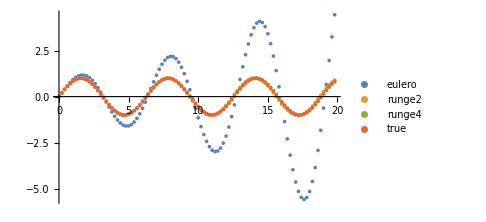

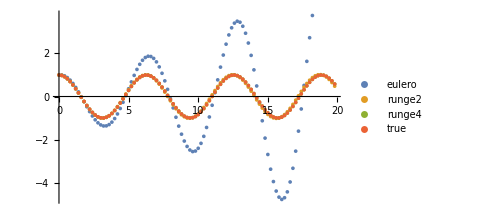

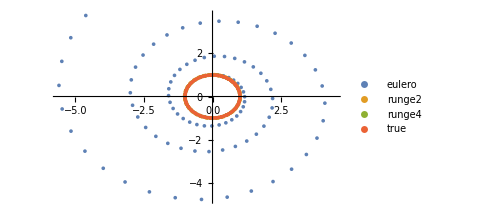

```mathematica
ListPlot[{X,Xk2,Xk4 , XT}, PlotLegends->{"eulero", "runge2", "runge4", "true"}, ImageSize->Medium]
ListPlot[{V,Vk2,Vk4, VT }, PlotLegends->{"eulero", "runge2", "runge4", "true"}, ImageSize->Medium] 
ListPlot[{K,Kk2,Kk4, KT }, PlotLegends->{"eulero", "runge2", "runge4", "true"}, ImageSize->Medium]
```

Posizione

-Graphics-

Velocita’

-Graphics-

Spazio delle fasi

-Graphics-

```mathematica
GraphicsRow[{ListLinePlot[{DX,DXk2,DXk4}, PlotLegends->{"eulero", "runge2", "runge4"}, ImageSize->Medium],ListPlot[{DX,DXk2,DXk4}, PlotLegends->{"eulero", "runge2", "runge4"}, ImageSize->Medium] },ImageSize->Full]
GraphicsRow[{ListLinePlot[{DV,DVk2,DVk4 }, PlotLegends->{"eulero", "runge2", "runge4"}, ImageSize->Medium],ListPlot[{DV,DVk2,DVk4}, PlotLegends->{"eulero", "runge2", "runge4"}, ImageSize->Medium] },ImageSize->Full]
GraphicsRow[{ListLinePlot[{DK,DKk2,DKk4 }, PlotLegends->{"eulero", "runge2", "runge4"}, ImageSize->Medium],ListPlot[{DK,DKk2,DKk4}, PlotLegends->{"eulero", "runge2", "runge4"}, ImageSize->Medium] },ImageSize->Full]
```

-Graphics-

-Graphics-

-Graphics-

Scarti dai valori veri

-Graphics-

-Graphics-

-Graphics-

-Graphics-